-Graphics3D-

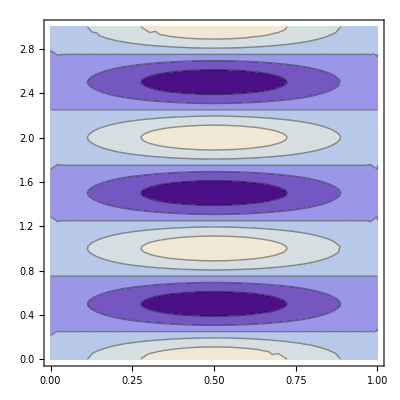

```mathematica
(*Зададим коэффициент уравнения*)
a=2;
(*Зададим длину струны*)
l=1;
(*Зададим начальные условия*)
phi[x_]=x*(1-x);
psy[x_]=0;
(*Зададим количество членов ряда Фурье*)
k=10;
(*Найдем коэффициенты ряда Фурье для функции u[x,t]*)A[n_]=1/l*Integrate[phi[x]*Sin[Pi*n*x/l],{x,0,l}];
B[n_]=1/(Pi*n*a)*Integrate[psy[x]*Sin[Pi*n*x/l],{x,0,l}];
(*Зададим решение задачи*)
u[x_,t_]=Sum[(A[n]*Cos[Pi*a*n*t/l]+B[n]*Sin[Pi*a*n*t/l])*Sin[Pi*n*x/l],{n,1,k}];
(*Зададим время наблюдения за колебаниями струны*)
T=3;
(*Построим график решения задачи*)
G=Plot3D[u[x,t],{x,0,l},{t,0,T}]
GC=ContourPlot[u[x,t],{x,0,l},{t,0,3}]
```

```mathematica
(*Выполним анимацию колебаний струны*)
Animate[Plot[u[x,t],{x,0,l},PlotRange->{-1,1}],{t,0,T},AnimationRunning->False]
```